```mathematica
F[x_]:=1/2 ⅈ (PolyLog[2,-ⅈ ⅇ^x]-PolyLog[2,ⅈ ⅇ^x])
```

```mathematica
G3[a_,b_]:=F[a-b]+F[b-a]-π/2(a+b);
```

```mathematica
EnergySetup[n_,FacesCW_]:=Module[{i,rhoV,rhoF,include,LineFaces,f,Faces,NM,nonlinefaces,radii,RADII},
Faces=Sort/@FacesCW;
f=Length[Faces];
LineFaces={};rhoV=Table[Subscript[rV, i],{i,1,n-2}];rhoF=Table[Subscript[rF, i],{i,1,f-2}];
include = {};
nonlinefaces={};
For[i=1,i≤f,i++,
If[!(Faces[[i,-2]]==n-1&&Faces[[i,-1]]==n),
(* then *) AppendTo[include,i];AppendTo[nonlinefaces,FacesCW[[i]]],
(* else *) AppendTo[LineFaces,i]]];

NM=NMinimize[{∑_(k=1)^(f-2) ∑_(i=1)^Length[Faces[[include[[k]]]]] If[Faces[[include[[k]],i]]<n-1,G3[Subscript[rV, Faces[[include[[k]],i]]],Subscript[rF, k]],0]+∑_(i=1)^(n-2) Subscript[rV, i] π If[MemberQ[Flatten@Table[Faces[[LineFaces[[m]]]],{m,1,2}],i],(* then *) 1,(* else *) 2]+∑_(j=1)^(f-2) Subscript[rF, j] π If[MemberQ[Faces[[include[[j]]]],n-1]||MemberQ[Faces[[include[[j]]]],n],(* then *) 1,(* else *) 2],
∑_(i=1)^(n-2) Subscript[rV, i]+∑_(j=1)^(f-2) Subscript[rF, j]==0},Join[rhoV,rhoF]];
RADII=Exp[Re[Join[rhoV,rhoF]/.(NM[[2]])]];
RADII/=RADII[[1]];
radii=<||>;
For[i=1,i≤n-2,i++,
radii[i]=RADII[[i]]
];
For[i=1,i≤Length[nonlinefaces],i++,
radii[nonlinefaces[[i]]]=RADII[[n-2+i]]
];
{radii,LineFaces}
];
```

```mathematica
Boundary[n_,FacesCW_,LineFaces_,radii_,ϵ_:0]:=Module[{i,j,faces,vertices,lastvisited,d,h,H,breaker,unvisited,f,endcircle,ComputeEndcircle,ComputeEndcircle2,delete},
unvisited =FacesCW;(*Keeps track of the faces we haven't visited*)
f=Length[FacesCW];

faces=<||>; (* centers of face circles (or normals, for lines) *)
For[i=1,i≤f,i++,faces[FacesCW[[i]]]={-∞,-∞}];
vertices=<||>; (* centers of vertex circles (or normals, for lines) *)
For[i=1,i≤n-2,i++,vertices[i]={-∞,-∞}];
(* Radii is an assoc from v->rad and facelist->rad *)

(*Vertex circles going vertically upwards along first FaceLine*)
h=0; (* height along the left line *)
For[i=1,i≤Length[FacesCW[[LineFaces[[1]]]]]-2(*Number of vertex circles that lie along first LineFace*),i++,
vertices[FacesCW[[LineFaces[[1]],i]]]={0,h+radii[FacesCW[[LineFaces[[1]],i]]]};(*Set the center of this vertex circle*)
h+=2radii[[FacesCW[[LineFaces[[1]],i]]]]];(*Keeps track of our cumulative height as we climb up the first FaceLine*)

unvisited=Delete[unvisited,Position[unvisited,FacesCW[[LineFaces[[1]]]]]];

d=0;(*Horizontal distance*)

ComputeEndcircle[prev_,face_]:=
(*Returns which vertex circle we calculated last based on previous vertex circle and face*)
If[face[[Mod[Position[face,n-1][[1,1]]-2,Length[face]]+1]]==prev,
(*then*)face[[Mod[Position[face,n-1][[1,1]],Length[face]]+1]],
(*else*) face[[Mod[Position[face,n-1][[1,1]]-2,Length[face]]+1]]];

endcircle=ComputeEndcircle[n,FacesCW[[LineFaces[[1]]]]];(*Previous vertex circle is bottom line, face is first FaceLine*)

(*Face circles going horizontally across upper vertex line*)
breaker=True;
For[j=1,j≤f ,j++,
For[i=1,i≤Length[unvisited],i++,
If[MemberQ[unvisited[[i]],n-1], (*determine if this face-circle contains n-1, so it is on the upper vertex line*)
If[MemberQ[unvisited[[i]],ComputeEndcircle[endcircle,unvisited[[i]]]],
(*determine if this face-circle also contains the vertex right before n-1 to ensure we are going horizontally across in the right order*)
If[unvisited[[i]]==FacesCW[[LineFaces[[2]]]],
(* If we've reached the second faceline, then do nothing--find the other face circle containing endcircle*)
,
(* else if the face circle is not a line*)
faces[unvisited[[i]]]={d+radii[unvisited[[i]]],h}; (*Set the center of this face circle*)
d+=2radii[unvisited[[i]]]; (* update how far along the top line we are *)
endcircle=ComputeEndcircle[endcircle,unvisited[[i]]];(*Update endcircle*)
unvisited=Delete[unvisited,i];] (* remove that face from the unvisited list *)
]
]
]
];
(*Vertex circles along the second FaceLine, climbing vertically upwards*)
h=0;
For[i=1,i≤Length[FacesCW[[LineFaces[[2]]]]]-2,i++,
vertices[FacesCW[[LineFaces[[2]],i]]]={d,h+radii[FacesCW[[LineFaces[[2]],i]]]};h+=2radii[[FacesCW[[LineFaces[[2]],i]]]]];
H=h;
h=0;(*Reset height*)

ComputeEndcircle2[prev_,face_]:=
If[face[[Mod[Position[face,n][[1,1]]-2,Length[face]]+1]]==prev,
(*then*)face[[Mod[Position[face,n][[1,1]],Length[face]]+1]],
(*else*) face[[Mod[Position[face,n][[1,1]]-2,Length[face]]+1]]];

endcircle=ComputeEndcircle2[n-1,FacesCW[[LineFaces[[1]]]]];
(*Face circles along lower vertex line, moving horizontally from origin to second FaceLine*)
d=0;(*Reset distance*)
breaker=True;
For[j=1,j≤f,j++,
For[i=1,i≤Length[unvisited],i++,
If[MemberQ[unvisited[[i]],n], (* determine if this face-circle contains n *)
If[MemberQ[unvisited[[i]],endcircle(* ComputeEndcircle2[endcircle,unvisited[[i]]] *)],(* determine if this face-cirlce also contains the vertex right before n *)
If[unvisited[[i]]==FacesCW[[LineFaces[[2]]]],
(* If we've reached the second faceline, then do nothing*)
,
(* else *)
faces[unvisited[[i]]]={d+radii[unvisited[[i]]],h}; (* then we'll make this face's center be where we know it is *)
d+=2radii[unvisited[[i]]]; (* update how far along the bottom line we are *)
endcircle=ComputeEndcircle2[endcircle,unvisited[[i]]];
unvisited=Delete[unvisited,i];] (* remove that face from the unvisited list *)
]
]
]
];
(*Set the normals of the vertex lines and face lines*)
faces[FacesCW[[LineFaces[[2]]]]]={1,0};
faces[FacesCW[[LineFaces[[1]]]]]={-1,0};
vertices[n]={0,-1};
vertices[n-1]={0,1};

If[ThrowOrderError[faces,vertices,radii,d,H,n,FacesCW[[LineFaces]],0],
faces[FacesCW[[LineFaces[[1]]]]]*=-1;
faces[FacesCW[[LineFaces[[2]]]]]*=-1;
For[i=1,i≤n,i++,
If[i==n-1||i==n,
,
If[Abs[vertices[i][[1]]-d]≤ϵ,
vertices[i]={0,vertices[i][[2]]},
If[Abs[vertices[i][[1]]-0]≤ϵ,
vertices[i]={d,vertices[i][[2]]}]];
]]];

(*Return the assoc's of the faces to their centers and vertices to their centers*)
{vertices,faces,d,H}
];
```

```mathematica
FindRest[{x_,y_},r_,face_,vertices_,radii_,lines_]:=(* face is all the vertices that the face intersects *)
(*{x_,y_},r: known center of opposite kind and its radius
face: all the circles of its kind that pass thru that opposite known circle
vertices: all the circles of its kind that are tangent to the one we'e looking for*)
Module[{verts=vertices,i,j,ϕ,θ,ω,face2=face,b,b2=True},

If[verts[face2[[1]]]=={-∞,-∞}||MemberQ[lines,face2[[1]]],
For[i=2,i≤Length[face2]&&b2,i++,
If[verts[face2[[i]]]≠{-∞,-∞}&&!MemberQ[lines,face2[[i]]],
face2=Join[face2[[i;;]],face2[[;;i-1]]];
b2=False;
]]];

b=True;
For[i=2,i≤Length[face2]&&b,i++,
If[MemberQ[lines,face2[[i]]],
AppendTo[face2,face2[[1]]];
For[j=Length[face2]-1,j>i,j--,
If[verts[face2[[j]]]=={-∞,-∞},
ϕ=ArcTan[verts[face2[[j+1]]][[1]]-x,verts[face2[[j+1]]][[2]]-y];
θ=ArcTan[radii[face2[[j+1]]]/r];(* j+1 refers to previously computed / known *)
ω=ArcTan[radii[face2[[j]]]/r];
verts[face2[[j]]]={x+√(r^2+radii[face2[[j]]]^2)Cos[ϕ-θ-ω],y+√(r^2+radii[face2[[j]]]^2)Sin[ϕ-θ-ω]}
]
];b=False;Break,
If[verts[face2[[i]]]=={-∞,-∞},
ϕ=ArcTan[verts[face2[[i-1]]][[1]]-x,verts[face2[[i-1]]][[2]]-y];
θ=ArcTan[radii[face2[[i-1]]]/r];(* i-1 refers to previously computed / known *)
ω=ArcTan[radii[face2[[i]]]/r];
verts[face2[[i]]]={x+√(r^2+radii[face2[[i]]]^2)Cos[ϕ+θ+ω],y+√(r^2+radii[face2[[i]]]^2)Sin[ϕ+θ+ω]}];
];];
verts
];
```

```mathematica
Cull[assoc_]:=Module[{vis={},unv={},i},For[i=1,i≤Length[Keys[assoc]],i++,If[assoc[Keys[assoc][[i]]]=={-∞,-∞},AppendTo[unv,Keys[assoc][[i]]],AppendTo[vis,Keys[assoc][[i]]]]];{vis,unv}]
```

```mathematica
Interior[n_,FacesCW_,LineFaces_,radii_,vertices_,faces_,d_,h_]:=
Module[{Vunv={},Funv={},Vvis={},Fvis={},i,j,f,verts=vertices,verts2,fcs=faces,fcs2,fi,vi,x,y,k,b},
f=Length[FacesCW];
For[i=1,i≤n,i++,
If[vertices[i]=={-∞,-∞},AppendTo[Vunv,i],AppendTo[Vvis,i]]];
For[i=1,i≤f,i++,
If[faces[FacesCW[[i]]]=={-∞,-∞},AppendTo[Funv,FacesCW[[i]]],AppendTo[Fvis,FacesCW[[i]]]]];

For[j=1,j≤n+Length[FacesCW]&&(Length[Vunv]+Length[Funv]>0),j++,

For[i=1,i≤Length[Fvis],i++,(* for a known face circle *)
If[Length[Intersection[Vvis,Fvis[[i]]]]*Length[Intersection[Vunv,Fvis[[i]]]]>0,
fi=Fvis[[i]];
{x,y}=fcs[fi];
verts2=FindRest[{x,y},radii[fi],fi,verts,radii,{n-1,n}];
If[ThrowOrderError[fcs,verts2,radii,d,h,n,{FacesCW[[LineFaces[[1]]]],FacesCW[[LineFaces[[2]]]]},0],verts=FindRest[{x,y},radii[fi],Reverse[fi],verts,radii,{n-1,n}],
verts=verts2];
];
{Vvis,Vunv}=Cull[verts];
];

For[i=1,i≤Length[Vvis],i++, (* for a known vertex circle *)
If[b=False;
For[k=1,k≤Length[Fvis],k++,b=b||If[MemberQ[Fvis[[k]],Vvis[[i]]],True,False]];b,
If[b=False;For[k=1,k≤Length[Funv],k++,b=b||If[MemberQ[Funv[[k]],Vvis[[i]]],True,False]];b,
(* then *)
vi=Vvis[[i]];
{x,y}=verts[vi];
fcs2=FindRest[{x,y},radii[vi],FacesList[vi,FacesCW],fcs,radii,FacesCW[[LineFaces]]];
If[ThrowOrderError[fcs2,verts,radii,d,h,n,FacesCW[[LineFaces]],0],
fcs=FindRest[{x,y},radii[vi],
Reverse[FacesList[vi,FacesCW]],fcs,radii,FacesCW[[LineFaces]]],
fcs=fcs2];
];
{Fvis,Funv}=Cull[fcs];
]
];
];
{verts,fcs}
];
```

```mathematica
ThrowOrderError[fcs2_,verts_,radii_,d_,h_,n_,fls_,ϵ_](* fcs2 is proposed fcs association. fls is facelines *):=
Module[{i,j,b,b2,K},
K={};
For[i=1,i≤Length[Keys[fcs2]],i++,
If[!MemberQ[fls,Keys[fcs2][[i]]],AppendTo[K,Keys[fcs2][[i]]]]
];

b=False; (* "breaker" *)
For[i=1,i≤Length[K]&&!b,i++,
If[b2=False;
-∞<fcs2[K[[i]]][[1]]<0
||-∞<fcs2[K[[i]]][[2]]<0
||fcs2[K[[i]]][[1]]>d
||fcs2[K[[i]]][[2]]>h
||(For[j=1,j≤Length[K[[i]]],j++,
If[K[[i,j]]≠n-1&&K[[i,j]]≠n&&verts[K[[i,j]]]≠{-∞,-∞}&&fcs2[K[[i]]]≠{-∞,-∞},
If[EuclideanDistance[verts[K[[i,j]]],fcs2[K[[i]]]]≥(1-ϵ)(radii[K[[i,j]]]+radii[K[[i]]]),b2=True;Break]]];b2),
b=True,

For[j=1,j≤Length[K]&&!b,j++,
If[i≠j&&fcs2[K[[i]]]≠{-∞,-∞}&&fcs2[K[[j]]]≠{-∞,-∞}&&
EuclideanDistance[fcs2[K[[i]]],fcs2[K[[j]]]]<(1+ϵ)(radii[fcs2[K[[i]]]]+radii[fcs2[K[[j]]]])
,(* then, bad *) b=True]]];
];


For[i=1,i≤Length[fls[[1]]]&&!b,i++,
If[verts[fls[[1,i]]][[1]]≠d/2+fcs2[fls[[1]]][[1]] d/2&&fls[[1,i]]<n-1,b=True]
];
For[i=1,i≤Length[fls[[2]]]&&!b,i++,
If[verts[fls[[2,i]]][[1]]≠d/2+fcs2[fls[[2]]][[1]] d/2&&fls[[2,i]]<n-1,b=True]
];

b
];
```

```mathematica
FacesList[v_,Faces_]:=
Module[{ContainV={},i,L=2,p=3,temp},
For[i=1,i≤Length[Faces],i++,
If[MemberQ[Faces[[i]],v],AppendTo[ContainV,Faces[[i]]]]];
While[L<Length[ContainV],
While[p≤Length[ContainV],
If[Length[Intersection[ContainV[[L-1]],ContainV[[p]]]]==2,
temp=ContainV[[p]];ContainV[[p]]=ContainV[[L]];ContainV[[L]]=temp;p=1+Length[ContainV],
p++]
];
L++;
p=L+1;
];
ContainV];
```

```mathematica
Q=({{0, 1/2, 0, 0}, {1/2, 0, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
```

```mathematica
InvCoords[z_,r_,d_:0]:=If[r==∞,{2d,0,z},{Norm[z]^2/r-r,1/r,z/r}];
```

```mathematica
Gram[SC_]:=SC.Q.Transpose[SC];
SuperCluster[vertices_,faces_,radii_,fls_,d_,h_,n_]:=
Module[{sc={},i},
For[i=1,i≤n-2,i++,AppendTo[sc,Flatten[InvCoords[vertices[i],radii[i]]]]];
AppendTo[sc,Flatten[InvCoords[vertices[n-1],∞,h/2+vertices[n-1][[2]] h/2]]];
AppendTo[sc,Flatten[InvCoords[vertices[n],∞,h/2+vertices[n][[2]] h/2]]];
For[i=1,i≤Length[Keys[faces]],i++,
If[!MemberQ[fls,Keys[faces][[i]]],
AppendTo[sc,Flatten[InvCoords[faces[Keys[faces][[i]]],radii[Keys[faces][[i]]]]]]
]];
AppendTo[sc,Flatten[InvCoords[faces[fls[[1]]],∞,d/2+faces[fls[[1]]][[1]] d/2]]];
AppendTo[sc,Flatten[InvCoords[faces[fls[[2]]],∞,d/2+faces[fls[[2]]][[1]] d/2]]];
sc
];
```

```mathematica
DrawCircle[{bhat_,b_,bx_,by_}]:=If[Abs[b]≥ .01,Circle[{bx,by}/b,1/b],InfiniteLine[{bx,by}bhat/2,{-by,bx}]];
```

```mathematica
Packing[n_,FacesCW_,ϵ_:0]:=
Module[{radii,LineFaces,vertices,faces,d,h},
{radii,LineFaces}=EnergySetup[n,FacesCW];
{vertices,faces,d,h}=Boundary[n,FacesCW,LineFaces,radii,ϵ];
{vertices,faces}=Interior[n,FacesCW,LineFaces,radii,vertices,faces,d,h];
{vertices,faces,radii,d,h,LineFaces}];
```

```mathematica
Render[radii_,fcs_,verts_,fls_,n_,d_,h_]:=Graphics[{Blue,Thick,
Table[If[i==n-1,Line[{{-Max[Values[radii]],h},{d+Max[Values[radii]],h}}],If[i==n,Line[{{-Max[Values[radii]],0},{d+Max[Values[radii]],0}}],
Circle[verts[Keys[verts][[i]]],radii[Keys[verts][[i]]]]]],{i,1,n}],
Red,Dashed,
Table[If[Keys[fcs][[i]]==fls[[1]],Line[{{0,-Max[Values[radii]]},{0,h+Max[Values[radii]]}}],
If[Keys[fcs][[i]]==fls[[2]],Line[{{d,-Max[Values[radii]]},{d,h+Max[Values[radii]]}}],
Circle[fcs[Keys[fcs][[i]]],radii[Keys[fcs][[i]]]]]],{i,1,Length[Keys[fcs]]}]
}];
```

```mathematica
SendToInt[ϵ_:0][y_]:=With[{x=Simplify[y]},If[Abs[x-Floor[x]]≤ϵ ,Floor[x],
If[Abs[x-Ceiling[x]]≤ ϵ ,Ceiling[x],x],x]];
```

```mathematica
R[vhat_]:=IdentityMatrix[4]+2Q.Transpose[{vhat}].{vhat}
BMat[n_]:=Table[b[i,j],{i,1,n},{j,1,n}];

Bend[V_,m_][i_]:=
Module[{sol,assignments,rest,l,others1,others2},
sol=Solve[BMat[m].(V[[;;m]])==(V[[;;m]]).R[V[[m+i]]]][[1]];
assignments=Association[sol];
rest=Complement[Flatten[BMat[m]],Keys[assignments]];
l=Length[rest];
others1=Solve[rest==Table[0,{j,1,l}]][[1]];
others2=<||>;
For[j=1,j≤l,j++,others2[rest[[j]]]=Subscript[a, j]];
others2=Normal[others2];
Column[{
MatrixForm[(BMat[m]/.assignments)/.others2],
MatrixForm[(BMat[m]/.assignments)/.others1]
}]
];
```

```mathematica
Everything[n_,FacesCW_,ϵ_:0,steps_,sizemax_:∞]:=Module[{vertices,faces,f=Length[FacesCW],radii,d,h,LineFaces,Vnye,Vout,bends={}},
{vertices,faces,radii,d,h,LineFaces}=Packing[n,FacesCW,ϵ];
Vnye=SendToInt[ϵ]//@SuperCluster[vertices,faces,radii,FacesCW[[LineFaces]],d,h,n];
Vout=MatrixForm[Simplify[RootApproximant[Vnye]]];
bends=Bend[Vout[[1]],n]/@Range@f;
Column[{
Render[radii,faces,vertices,FacesCW[[LineFaces]],n,d,h],
Graphics[{Thick, DrawCircle/@Orbit[Vnye[[-f;;]],Vnye[[;;n]],steps,sizemax],Red,DrawCircle/@Vnye[[-f;;]], Blue, DrawCircle/@Vnye[[;;n]]},PlotRange->{{-d,2 d},{-1.2 Max[Values[radii]],h+1.2 Max[Values[radii]]}},PlotRangeClipping->True],
Vout,
bends,
MatrixForm[Simplify[RootApproximant[
SendToInt[ϵ]//@Gram[SuperCluster[vertices,faces,radii,FacesCW[[LineFaces]],d,h,n]]]
]]
}]]
```

```mathematica
Orbit[co_,cl_,steps_,sizemax_:∞]:=Module[{i,j,k,orbit=cl,L},
For[i=1,i≤steps,i++,
L=Length[orbit];
For[j=1,j≤Length[co],j++,
For[k=1,k≤L,k++,
If[(orbit⟦k⟧.R[co⟦j⟧])⟦2⟧≤sizemax&&!MemberQ[Round[N[orbit],.01],Round[N[orbit⟦k⟧.R[co⟦j⟧]],.01](*new thing*)],AppendTo[orbit,orbit⟦k⟧.R[co⟦j⟧](*newthing*)]]
]
]
];
orbit
];
```

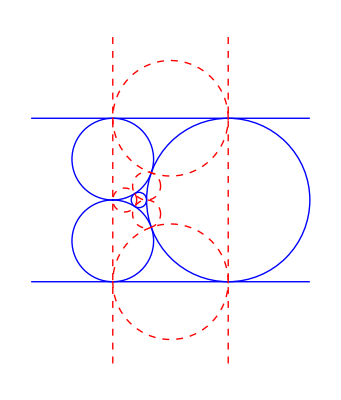
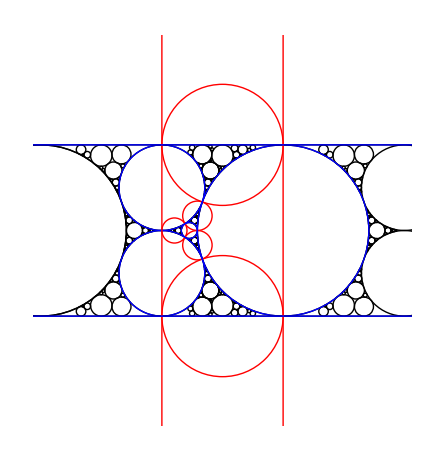
-Graphics-
-Graphics-
(1/11 (680+√471255) | 1 | 34009/9961 | 18106/1699
Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] | 1801/19193 | 9273/6557 | 1
0 | Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | 0 | 1
5744145321 | 1/5 (126446577+√15988736921367074) | 0 | 269504641+2 √18158187847746903
Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] | Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] | 0 | 3
Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | 0 | 0 | 1
0 | 0 | 0 | -1
Root[36+749 #1-1684 #1^2+23 #1^3&,3] | Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3] | 1 | 9512/1393
Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] | Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1] | 11243/4657 | 9512/1393
Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] | Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1] | 1 | 9512/3363
0 | Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2] | 1 | 0
Root[-194-647 #1-399 #1^2+8 #1^3&,3] | 7338/13417 | 14198/5881 | 8696/1801
Root[20+21 #1+8 #1^2-151 #1^3+5 #1^4&,2] | 0 | 1 | 0
0 | 0 | -1 | 0)
{(a_1 | (6557 (-5518136305231+37046064671 Root[36+749 #1-1684 #1^2+23 #1^3&,3]+2290120361480 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+3367824061 √471255 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]))/343528157694183-(222997013 a_1)/92368353 | -(-71757873906497254586+437482793931992347 Root[36+749 #1-1684 #1^2+23 #1^3&,3]+1031655089290195349830 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+39771163084726577 √471255 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-6593335930624454319 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-407588039347693539720 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2-599394175511314029 √471255 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2)/(6593335930624454319 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_1)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_2)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_3)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_2 | a_3 | -(-21236286112004040-31229832517653 √471255+52342557098555790 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-343528157694183 Root[36+749 #1-1684 #1^2+23 #1^3&,3]^2-36182419753399667 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]+242911046047747 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]-21236286112004040 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-31229832517653 √471255 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+15016319210224360 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+22082822367977 √471255 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/(343528157694183 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_1)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_2)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_3)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | -(-99958718351750675638298 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+609413531947265339371 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1437095539381242122313190 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+55401230177024121761 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-9184516951359864866367 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-567770138811337100829960 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2-834956086487260442397 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2-567770138811337100829960 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-834956086487260442397 √471255 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+1399422702860865719515710 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-9184516951359864866367 Root[36+749 #1-1684 #1^2+23 #1^3&,3]^2 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-8490611168596455330486659 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+56221378324535198900125 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-967367710981510733562283 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+6494433047564610582203 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-567770138811337100829960 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-834956086487260442397 √471255 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+3475503387334903204735000 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+5111034393139563536375 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+401474042940357745081640 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+590403004324055507473 √471255 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/(9184516951359864866367 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((2329682695638484 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+186198282022701480 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+273821002974561 √471255 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-24827095060834883 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-7271688858194791 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_1)/(3012031032720171 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+√15988736921367074 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+28720726605 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-1347523205 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-10 √18158187847746903 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_2)/(5 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]-3 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_3)/(Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])
a_4 | (-2642063410801+16450155701 Root[36+749 #1-1684 #1^2+23 #1^3&,3]+175306961893 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/247921527777-(222997013 a_4)/92368353 | -(-34128285867302958746+194262471347554057 Root[36+749 #1-1684 #1^2+23 #1^3&,3]+514349950627980808242 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-2927744245198453989 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+2070227436187454201 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-31200552636365312277 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2)/(31200552636365312277 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_4)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_5)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_6)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_5 | a_6 | -(26798830335433794 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-152542293815373 Root[36+749 #1-1684 #1^2+23 #1^3&,3]^2-18949631242255946 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]+107863670931457 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]-1625621457633789 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+1149487749132401 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]^2 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/(1625621457633789 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_4)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_5)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_6)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | (27245334137836987-156473881027912 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-1667519821526216 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/244202597916949-((150574946 Root[36+749 #1-1684 #1^2+23 #1^3&,3])/9133901-(1801 Root[36+749 #1-1684 #1^2+23 #1^3&,3]^2)/19193-Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (1+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+((2642063410801-16450155701 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-175306961893 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]) (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/247921527777-(-16450155701+2889984938578 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-16450155701 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-175306961893 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2)/(175306961893 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_4-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_5-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_6
a_7 | (6557 (-19024+1393 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/12917289-(222997013 a_7)/92368353 | 1+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-(19024 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/(1393 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(11809157 (-19024+1393 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/(247921527777 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_7)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_8)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_9)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_8 | a_9 | -(6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (-19024+1393 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/(12917289 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(19024 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-1393 Root[36+749 #1-1684 #1^2+23 #1^3&,3]^2 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/(1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_7)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_8)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_9)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | 1+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-(19024 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/(1393 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])+(179015839-13250216 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/1940449-(6557 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) (-19024+1393 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/12917289-(19024 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-1393 Root[36+749 #1-1684 #1^2+23 #1^3&,3]^2 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/(1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_7-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_8-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_9
a_10 | -(6557 (25635281451920+190240 √18158187847746903-176140081761 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-1393 √15988736921367074 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-40007972160765 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]))/64586445-(222997013 a_10)/92368353 | -(-334079891956923300769-247921527777 √15988736921367074-2246574027680 √18158187847746903+2080065879508485477 Root[36+749 #1-1684 #1^2+23 #1^3&,3]+16450155701 √15988736921367074 Root[36+749 #1-1684 #1^2+23 #1^3&,3]+5034942938893937417985 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+33858285315360 √18158187847746903 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-31348828552012069329 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-247921527777 √15988736921367074 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-7120486418777130407085 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2)/(1239607638885 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_10)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_11)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_12)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_11 | a_12 | (6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (25635281451920+190240 √18158187847746903-176140081761 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-1393 √15988736921367074 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-40007972160765 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]))/(64586445 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((19024 (269504641+2 √18158187847746903) Root[36+749 #1-1684 #1^2+23 #1^3&,3])/1393-1/5 (126446577+√15988736921367074) Root[36+749 #1-1684 #1^2+23 #1^3&,3]^2-5744145321 (1+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_10)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_11)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_12)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | (241227997115043995+1790158390 √18158187847746903-1675444457710632 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-13250216 √15988736921367074 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-380555831193196680 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/9702245-((19024 (269504641+2 √18158187847746903) Root[36+749 #1-1684 #1^2+23 #1^3&,3])/1393-1/5 (126446577+√15988736921367074) Root[36+749 #1-1684 #1^2+23 #1^3&,3]^2-5744145321 (1+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(6557 (25635281451920+190240 √18158187847746903-176140081761 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-1393 √15988736921367074 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-40007972160765 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]) (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/64586445-((19024 (269504641+2 √18158187847746903) Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/1393-5744145321 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2-1/5 (126446577+√15988736921367074) (1+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]))/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_10-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_11-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_12
a_13 | (6557 (-57072+1393 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+1393 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]))/12917289-(222997013 a_13)/92368353 | -(-673972208304+10157485594608 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+16450155701 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-247921527777 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2-247921527777 Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+16450155701 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]-247921527777 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3])/(247921527777 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_13)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_14)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_15)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_14 | a_15 | -(6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (-57072+1393 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+1393 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]))/(12917289 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((57072 Root[36+749 #1-1684 #1^2+23 #1^3&,3])/1393-Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] (1+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])-Root[36+749 #1-1684 #1^2+23 #1^3&,3]^2 Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3])/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_13)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_14)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_15)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | (537047517-13250216 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-13250216 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3])/1940449-((57072 Root[36+749 #1-1684 #1^2+23 #1^3&,3])/1393-Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] (1+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])-Root[36+749 #1-1684 #1^2+23 #1^3&,3]^2 Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3])/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(6557 (-57072+1393 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+1393 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]) (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/12917289-((57072 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/1393-Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2-(1+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]) Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3])/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_13-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_14-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_15
a_16 | (6557 (-19024+1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]))/12917289-(222997013 a_16)/92368353 | -(-224657402768+3385828531536 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+16450155701 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-247921527777 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2)/(247921527777 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_16)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_17)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_18)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_17 | a_18 | 1-(19024 Root[36+749 #1-1684 #1^2+23 #1^3&,3])/(1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-(6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (-19024+1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]))/(12917289 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_16)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_17)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_18)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | 1-(19024 Root[36+749 #1-1684 #1^2+23 #1^3&,3])/(1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+(179015839-13250216 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/1940449-(6557 (-19024+1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]) (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/12917289-(19024 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2)/(1393 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_16-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_17-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_18
a_19 | 124740368/12917289-(222997013 a_19)/92368353 | (19024 (-11809157+177976689 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]))/(247921527777 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_19)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_20)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_21)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_20 | a_21 | (19024 (9273 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]))/(12917289 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_19)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_20)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_21)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | -179015839/1940449+(19024 Root[36+749 #1-1684 #1^2+23 #1^3&,3])/(1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(124740368 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/12917289+(19024 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/(1393 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_19-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_20-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_21)
(0 | (6557 (-5518136305231+37046064671 Root[36+749 #1-1684 #1^2+23 #1^3&,3]+2290120361480 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+3367824061 √471255 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]))/343528157694183 | -(-71757873906497254586+437482793931992347 Root[36+749 #1-1684 #1^2+23 #1^3&,3]+1031655089290195349830 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+39771163084726577 √471255 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-6593335930624454319 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-407588039347693539720 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2-599394175511314029 √471255 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2)/(6593335930624454319 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | -(-21236286112004040-31229832517653 √471255+52342557098555790 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-343528157694183 Root[36+749 #1-1684 #1^2+23 #1^3&,3]^2-36182419753399667 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]+242911046047747 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]-21236286112004040 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-31229832517653 √471255 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+15016319210224360 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+22082822367977 √471255 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/(343528157694183 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]) | -(-99958718351750675638298 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+609413531947265339371 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1437095539381242122313190 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+55401230177024121761 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-9184516951359864866367 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-567770138811337100829960 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2-834956086487260442397 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2-567770138811337100829960 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-834956086487260442397 √471255 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+1399422702860865719515710 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-9184516951359864866367 Root[36+749 #1-1684 #1^2+23 #1^3&,3]^2 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-8490611168596455330486659 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+56221378324535198900125 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-967367710981510733562283 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+6494433047564610582203 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-567770138811337100829960 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-834956086487260442397 √471255 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+3475503387334903204735000 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+5111034393139563536375 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+401474042940357745081640 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+590403004324055507473 √471255 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/(9184516951359864866367 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])
0 | (-2642063410801+16450155701 Root[36+749 #1-1684 #1^2+23 #1^3&,3]+175306961893 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/247921527777 | -(-34128285867302958746+194262471347554057 Root[36+749 #1-1684 #1^2+23 #1^3&,3]+514349950627980808242 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-2927744245198453989 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+2070227436187454201 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-31200552636365312277 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2)/(31200552636365312277 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | -(26798830335433794 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-152542293815373 Root[36+749 #1-1684 #1^2+23 #1^3&,3]^2-18949631242255946 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]+107863670931457 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]-1625621457633789 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+1149487749132401 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]^2 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/(1625621457633789 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]) | (27245334137836987-156473881027912 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-1667519821526216 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/244202597916949-((150574946 Root[36+749 #1-1684 #1^2+23 #1^3&,3])/9133901-(1801 Root[36+749 #1-1684 #1^2+23 #1^3&,3]^2)/19193-Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (1+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+((2642063410801-16450155701 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-175306961893 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]) (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/247921527777-(-16450155701+2889984938578 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-16450155701 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-175306961893 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2)/(175306961893 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])
0 | (6557 (-19024+1393 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/12917289 | 1+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-(19024 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/(1393 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(11809157 (-19024+1393 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/(247921527777 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | -(6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (-19024+1393 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/(12917289 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(19024 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-1393 Root[36+749 #1-1684 #1^2+23 #1^3&,3]^2 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/(1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]) | 1+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-(19024 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/(1393 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])+(179015839-13250216 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/1940449-(6557 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) (-19024+1393 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/12917289-(19024 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-1393 Root[36+749 #1-1684 #1^2+23 #1^3&,3]^2 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/(1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])
0 | -(6557 (25635281451920+190240 √18158187847746903-176140081761 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-1393 √15988736921367074 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-40007972160765 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]))/64586445 | -(-334079891956923300769-247921527777 √15988736921367074-2246574027680 √18158187847746903+2080065879508485477 Root[36+749 #1-1684 #1^2+23 #1^3&,3]+16450155701 √15988736921367074 Root[36+749 #1-1684 #1^2+23 #1^3&,3]+5034942938893937417985 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+33858285315360 √18158187847746903 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-31348828552012069329 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-247921527777 √15988736921367074 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-7120486418777130407085 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2)/(1239607638885 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | (6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (25635281451920+190240 √18158187847746903-176140081761 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-1393 √15988736921367074 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-40007972160765 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]))/(64586445 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((19024 (269504641+2 √18158187847746903) Root[36+749 #1-1684 #1^2+23 #1^3&,3])/1393-1/5 (126446577+√15988736921367074) Root[36+749 #1-1684 #1^2+23 #1^3&,3]^2-5744145321 (1+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | (241227997115043995+1790158390 √18158187847746903-1675444457710632 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-13250216 √15988736921367074 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-380555831193196680 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/9702245-((19024 (269504641+2 √18158187847746903) Root[36+749 #1-1684 #1^2+23 #1^3&,3])/1393-1/5 (126446577+√15988736921367074) Root[36+749 #1-1684 #1^2+23 #1^3&,3]^2-5744145321 (1+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(6557 (25635281451920+190240 √18158187847746903-176140081761 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-1393 √15988736921367074 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-40007972160765 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]) (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/64586445-((19024 (269504641+2 √18158187847746903) Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/1393-5744145321 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2-1/5 (126446577+√15988736921367074) (1+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]))/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]
0 | (6557 (-57072+1393 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+1393 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]))/12917289 | -(-673972208304+10157485594608 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+16450155701 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-247921527777 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2-247921527777 Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+16450155701 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]-247921527777 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3])/(247921527777 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | -(6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (-57072+1393 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+1393 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]))/(12917289 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((57072 Root[36+749 #1-1684 #1^2+23 #1^3&,3])/1393-Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] (1+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])-Root[36+749 #1-1684 #1^2+23 #1^3&,3]^2 Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3])/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | (537047517-13250216 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-13250216 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3])/1940449-((57072 Root[36+749 #1-1684 #1^2+23 #1^3&,3])/1393-Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] (1+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])-Root[36+749 #1-1684 #1^2+23 #1^3&,3]^2 Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3])/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(6557 (-57072+1393 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+1393 Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]) (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/12917289-((57072 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/1393-Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2-(1+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]) Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3])/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]
0 | (6557 (-19024+1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]))/12917289 | -(-224657402768+3385828531536 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+16450155701 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-247921527777 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2)/(247921527777 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | 1-(19024 Root[36+749 #1-1684 #1^2+23 #1^3&,3])/(1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-(6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (-19024+1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]))/(12917289 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]) | 1-(19024 Root[36+749 #1-1684 #1^2+23 #1^3&,3])/(1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])+Root[36+749 #1-1684 #1^2+23 #1^3&,3] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]+(179015839-13250216 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/1940449-(6557 (-19024+1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]) (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/12917289-(19024 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]-1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]^2)/(1393 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])
0 | 124740368/12917289 | (19024 (-11809157+177976689 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3]))/(247921527777 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | (19024 (9273 Root[36+749 #1-1684 #1^2+23 #1^3&,3]-6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]))/(12917289 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]) | -179015839/1940449+(19024 Root[36+749 #1-1684 #1^2+23 #1^3&,3])/(1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(124740368 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/12917289+(19024 Root[-2+3 #1+62 #1^2-108 #1^3+17 #1^4-#1^5+4 #1^6&,3])/(1393 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])),(a_1 | (6557 (-311532798414168947583+1939681971032318821 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]+119907612754725163480 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+176334724639301711 √471255 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/7450318105688090245767-(222997013 a_1)/92368353 | -(-3821933682524743642619423562+22906008925990105031243897 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]+24584526138205752885516385634 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+2082364447817282275567627 √471255 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-142993955402471516087006031 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-8839626333970966449014918280 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2-12999450491133774189727821 √471255 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2)/(142993955402471516087006031 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_1)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_2)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_3)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_2 | a_3 | -(-460565119260718306101960-677301645971644567797 √471255+1207133763022456152666618 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-7450318105688090245767 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]^2-2042720559201705789301731 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]+12718494684058914509297 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]-460565119260718306101960 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-677301645971644567797 √471255 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+786234216832732896938360 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+1156226789459901319027 √471255 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/(7450318105688090245767 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_1)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_2)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_3)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | -(-5323953619756967894168857021866 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+31908070433904216308522748521 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-12313599483221556263477781164040 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-18108234534149347446290854653 √471255 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+32273746010970171306815646188682 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-199190579875642821909199401183 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]^2 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-163642332259366434503368347455667 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+1020118750408007215595127678719 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-54613868420012366525196895454619 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+340039753380301845424473688153 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+34246244910520613769524325188162 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+2900733675809474209865704411 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-199190579875642821909199401183 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-12313599483221556263477781164040 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-18108234534149347446290854653 √471255 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+63061886388858627873153347411720 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+92738068218909746872284334429 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+21020639299873204989876555267640 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+30912704852754713220406698923 √471255 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-12313599483221556263477781164040 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2-18108234534149347446290854653 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2)/(199190579875642821909199401183 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((2329682695638484 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+186198282022701480 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+273821002974561 √471255 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-24827095060834883 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-7271688858194791 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_1)/(3012031032720171 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+√15988736921367074 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+28720726605 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-1347523205 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-10 √18158187847746903 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_2)/(5 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]-3 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_3)/(Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])
a_4 | (-182654269957378206497+861307961244319351 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]+9178836035625886343 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/5376835073971326273-(222997013 a_4)/92368353 | -(-2220488840198696554357574890+10171320939684082574097107 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]+13861711274668664962410490470 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-63495889551634005456081861 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+108394315821963685088642851 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-676666634183515528438966773 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2)/(676666634183515528438966773 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_4)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_5)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_6)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_5 | a_6 | -(722227440976849109696790 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-3308283725922680428077 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]^2-1232919955690558886372890 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]+5647596301879001984507 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]-35255907580029986372061 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+60185627885598936751051 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]^2 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/(35255907580029986372061 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_4)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_5)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_6)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | ((-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) (182654269957378206497-861307961244319351 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-9178836035625886343 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/5376835073971326273+(157944121005120510187-728698863946986184 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-7765639808847587912 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/1137251498499231493-(-76608375099557+16724282222836390 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-76608375099557 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-816404521535701 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2)/(816404521535701 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((871374054230 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2])/42536576957-(1801 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]^2)/19193-Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (1+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_4-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_5-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_6
a_7 | (73720351 (-19024+1393 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/60155814873-(222997013 a_7)/92368353 | 1-(132770352151 (-19024+1393 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/(1154570554857489 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-(19024 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/(1393 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_7)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_8)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_9)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_8 | a_9 | -(73720351 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (-19024+1393 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/(60155814873 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(19024 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-1393 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]^2 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/(1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_7)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_8)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_9)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | 1+(179015839-13250216 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/1940449-(73720351 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) (-19024+1393 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/60155814873-(19024 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-1393 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]^2 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/(1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-(19024 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/(1393 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_7-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_8-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_9
a_10 | -(73720351 (25635281451920+190240 √18158187847746903-176140081761 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-1393 √15988736921367074 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-40007972160765 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/300779074365-(222997013 a_10)/92368353 | (132770352151 (25635281451920+190240 √18158187847746903-176140081761 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-1393 √15988736921367074 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-40007972160765 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/(5772852774287445 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((19024 (269504641+2 √18158187847746903) Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/1393-5744145321 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2-1/5 (126446577+√15988736921367074) (1+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-(1371208178716 a_10)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_11)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_12)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_11 | a_12 | (73720351 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (25635281451920+190240 √18158187847746903-176140081761 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-1393 √15988736921367074 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-40007972160765 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/(300779074365 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((19024 (269504641+2 √18158187847746903) Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2])/1393-1/5 (126446577+√15988736921367074) Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]^2-5744145321 (1+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_10)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_11)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_12)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | (241227997115043995+1790158390 √18158187847746903-1675444457710632 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-13250216 √15988736921367074 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-380555831193196680 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/9702245+(73720351 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) (25635281451920+190240 √18158187847746903-176140081761 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-1393 √15988736921367074 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-40007972160765 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/300779074365-((19024 (269504641+2 √18158187847746903) Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2])/1393-1/5 (126446577+√15988736921367074) Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]^2-5744145321 (1+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-((19024 (269504641+2 √18158187847746903) Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/1393-5744145321 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2-1/5 (126446577+√15988736921367074) (1+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_10-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_11-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_12
a_13 | (73720351 (-57072+1393 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+1393 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/60155814873-(222997013 a_13)/92368353 | -(-7577469537961872-1154570554857489 Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+184949100546343 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+47303410414089456 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+184949100546343 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-1154570554857489 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-1154570554857489 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2)/(1154570554857489 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_13)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_14)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_15)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_14 | a_15 | -(73720351 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (-57072+1393 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+1393 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/(60155814873 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((57072 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2])/1393-Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]^2 Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]-Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] (1+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_13)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_14)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_15)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | (537047517-13250216 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]-13250216 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/1940449-(73720351 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) (-57072+1393 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+1393 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/60155814873-((57072 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2])/1393-Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]^2 Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]-Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] (1+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-((57072 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/1393-Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2-Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] (1+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_13-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_14-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_15
a_16 | (73720351 (-19024+1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/60155814873-(222997013 a_16)/92368353 | -(-2525823179320624+15767803471363152 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+184949100546343 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-1154570554857489 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2)/(1154570554857489 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_16)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_17)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_18)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_17 | a_18 | 1-(19024 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2])/(1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-(73720351 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (-19024+1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/(60155814873 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_16)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_17)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_18)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | 1-(19024 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2])/(1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+(179015839-13250216 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/1940449-(73720351 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) (-19024+1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/60155814873-(19024 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2)/(1393 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_16-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_17-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_18
a_19 | 1402455957424/60155814873-(222997013 a_19)/92368353 | (19024 (-132770352151+828837440673 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/(1154570554857489 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_19)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_20)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_21)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_20 | a_21 | (19024 (43184361 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-73720351 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]))/(60155814873 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_19)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_20)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_21)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | -179015839/1940449+(19024 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2])/(1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(1402455957424 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/60155814873+(19024 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/(1393 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_19-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_20-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_21)
(0 | (6557 (-311532798414168947583+1939681971032318821 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]+119907612754725163480 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+176334724639301711 √471255 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/7450318105688090245767 | -(-3821933682524743642619423562+22906008925990105031243897 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]+24584526138205752885516385634 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+2082364447817282275567627 √471255 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-142993955402471516087006031 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-8839626333970966449014918280 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2-12999450491133774189727821 √471255 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2)/(142993955402471516087006031 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | -(-460565119260718306101960-677301645971644567797 √471255+1207133763022456152666618 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-7450318105688090245767 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]^2-2042720559201705789301731 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]+12718494684058914509297 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]-460565119260718306101960 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-677301645971644567797 √471255 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+786234216832732896938360 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+1156226789459901319027 √471255 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/(7450318105688090245767 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]) | -(-5323953619756967894168857021866 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+31908070433904216308522748521 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-12313599483221556263477781164040 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-18108234534149347446290854653 √471255 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+32273746010970171306815646188682 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-199190579875642821909199401183 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]^2 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-163642332259366434503368347455667 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+1020118750408007215595127678719 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-54613868420012366525196895454619 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+340039753380301845424473688153 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+34246244910520613769524325188162 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+2900733675809474209865704411 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-199190579875642821909199401183 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-12313599483221556263477781164040 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-18108234534149347446290854653 √471255 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+63061886388858627873153347411720 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+92738068218909746872284334429 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+21020639299873204989876555267640 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+30912704852754713220406698923 √471255 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-12313599483221556263477781164040 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2-18108234534149347446290854653 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2)/(199190579875642821909199401183 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])
0 | (-182654269957378206497+861307961244319351 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]+9178836035625886343 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/5376835073971326273 | -(-2220488840198696554357574890+10171320939684082574097107 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]+13861711274668664962410490470 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-63495889551634005456081861 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+108394315821963685088642851 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-676666634183515528438966773 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2)/(676666634183515528438966773 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | -(722227440976849109696790 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-3308283725922680428077 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]^2-1232919955690558886372890 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]+5647596301879001984507 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]-35255907580029986372061 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+60185627885598936751051 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]^2 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/(35255907580029986372061 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]) | ((-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) (182654269957378206497-861307961244319351 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-9178836035625886343 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/5376835073971326273+(157944121005120510187-728698863946986184 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-7765639808847587912 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/1137251498499231493-(-76608375099557+16724282222836390 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-76608375099557 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-816404521535701 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2)/(816404521535701 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((871374054230 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2])/42536576957-(1801 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]^2)/19193-Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (1+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]
0 | (73720351 (-19024+1393 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/60155814873 | 1-(132770352151 (-19024+1393 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/(1154570554857489 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-(19024 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/(1393 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | -(73720351 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (-19024+1393 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/(60155814873 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(19024 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-1393 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]^2 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/(1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]) | 1+(179015839-13250216 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/1940449-(73720351 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) (-19024+1393 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/60155814873-(19024 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-1393 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]^2 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/(1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-(19024 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/(1393 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])
0 | -(73720351 (25635281451920+190240 √18158187847746903-176140081761 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-1393 √15988736921367074 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-40007972160765 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/300779074365 | (132770352151 (25635281451920+190240 √18158187847746903-176140081761 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-1393 √15988736921367074 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-40007972160765 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/(5772852774287445 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((19024 (269504641+2 √18158187847746903) Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/1393-5744145321 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2-1/5 (126446577+√15988736921367074) (1+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | 0 | 0 | (73720351 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (25635281451920+190240 √18158187847746903-176140081761 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-1393 √15988736921367074 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-40007972160765 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/(300779074365 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((19024 (269504641+2 √18158187847746903) Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2])/1393-1/5 (126446577+√15988736921367074) Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]^2-5744145321 (1+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | (241227997115043995+1790158390 √18158187847746903-1675444457710632 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-13250216 √15988736921367074 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-380555831193196680 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/9702245+(73720351 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) (25635281451920+190240 √18158187847746903-176140081761 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-1393 √15988736921367074 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-40007972160765 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/300779074365-((19024 (269504641+2 √18158187847746903) Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2])/1393-1/5 (126446577+√15988736921367074) Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]^2-5744145321 (1+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-((19024 (269504641+2 √18158187847746903) Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/1393-5744145321 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2-1/5 (126446577+√15988736921367074) (1+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]
0 | (73720351 (-57072+1393 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+1393 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/60155814873 | -(-7577469537961872-1154570554857489 Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+184949100546343 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+47303410414089456 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+184949100546343 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-1154570554857489 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-1154570554857489 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2)/(1154570554857489 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | -(73720351 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (-57072+1393 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+1393 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/(60155814873 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((57072 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2])/1393-Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]^2 Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]-Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] (1+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | (537047517-13250216 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]-13250216 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/1940449-(73720351 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) (-57072+1393 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+1393 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/60155814873-((57072 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2])/1393-Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]^2 Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]-Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] (1+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-((57072 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/1393-Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2-Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] (1+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]
0 | (73720351 (-19024+1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/60155814873 | -(-2525823179320624+15767803471363152 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+184949100546343 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-1154570554857489 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2)/(1154570554857489 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | 1-(19024 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2])/(1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-(73720351 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (-19024+1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/(60155814873 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]) | 1-(19024 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2])/(1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])+Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]+(179015839-13250216 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/1940449-(73720351 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) (-19024+1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/60155814873-(19024 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]-1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]^2)/(1393 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])
0 | 1402455957424/60155814873 | (19024 (-132770352151+828837440673 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1]))/(1154570554857489 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | (19024 (43184361 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2]-73720351 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]))/(60155814873 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]) | -179015839/1940449+(19024 Root[698-251 #1+277 #1^2-97 #1^3+#1^4&,2])/(1393 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(1402455957424 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/60155814873+(19024 Root[-1+2 #1-#1^3+2 #1^6+#1^8+#1^9+#1^10+#1^11-#1^12+#1^13+4 #1^15&,1])/(1393 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])),(a_1 | (6557 (-39879074712587+626059876827 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]+38701883294760 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]+56914534257 √471255 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/5805453237816771-(222997013 a_1)/92368353 | -(-582362318289087044962+7393239376850704839 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]+7935008053451394186270 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]+672112670622791349 √471255 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-111424063993417285803 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-6888033046865795849640 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2-10129460363037935073 √471255 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2)/(111424063993417285803 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_1)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_2)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_3)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_2 | a_3 | -(-358882563792309480-527768476165161 √471255+389619727891830150 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-5805453237816771 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]^2-261487092890432959 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]+4105074612354639 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]-358882563792309480 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-527768476165161 √471255 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]+253768248763741320 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]+373188601123149 √471255 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/(5805453237816771 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_1)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_2)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_3)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | -(-652828158802066577402402 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+8287821341449640124519 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]+8895144027919012882808670 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]+753438303768149102229 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-124906375736620777385163 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-7721485045536557147446440 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2-11355125066965525216833 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2-7721485045536557147446440 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-11355125066965525216833 √471255 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-16753058281004412537585151 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+8382805981356671493292950 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+264966436192313521580145 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-124906375736620777385163 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]^2 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-5625987108481455435719527 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+88322129376148219272567 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+16379743328252108606772600 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+24087857835664865598195 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-7721485045536557147446440 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-11355125066965525216833 √471255 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+5459913452343708100485960 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+8029284488740747206597 √471255 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/(124906375736620777385163 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((2329682695638484 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+186198282022701480 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+273821002974561 √471255 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-24827095060834883 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-7271688858194791 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_1)/(3012031032720171 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+√15988736921367074 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+28720726605 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-1347523205 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-10 √18158187847746903 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_2)/(5 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]-3 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_3)/(Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])
a_4 | (-2992677488131+39714194991 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]+423228508863 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/598535605107-(222997013 a_4)/92368353 | -(-42409199238503180366+468991163777332587 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]+639152215827947528982 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-7068200930798564799 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]+4997971908039058491 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-75324808697843894607 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2)/(75324808697843894607 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_4)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_5)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_6)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_5 | a_6 | -(33301319013595974 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-368269730151543 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]^2-23547584252361566 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]+260405976555987 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]-3924597962686599 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]+2775109332614691 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]^2 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/(3924597962686599 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_4)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_5)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_6)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | (32736301467573587-377761422754392 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-4025749576304856 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/1423317475306269-((187110566 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4])/22051191-(1801 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]^2)/19193-Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (1+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+((2992677488131-39714194991 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-423228508863 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]) (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/598535605107-(-39714194991+3591213093238 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-39714194991 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-423228508863 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2)/(423228508863 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_4-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_5-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_6
a_7 | (6557 (-19024+3363 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/31185099-(222997013 a_7)/92368353 | 1+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-(19024 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/(3363 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(11809157 (-19024+3363 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/(598535605107 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_7)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_8)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_9)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_8 | a_9 | -(6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (-19024+3363 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/(31185099 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(19024 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-3363 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]^2 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/(3363 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_7)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_8)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_9)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | 1+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-(19024 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/(3363 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])+(169646519-31988856 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/11309769-(6557 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) (-19024+3363 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/31185099-(19024 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-3363 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]^2 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/(3363 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_7-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_8-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_9
a_10 | -(6557 (25635281451920+190240 √18158187847746903-425239838451 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-3363 √15988736921367074 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-96587803572615 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/155925495-(222997013 a_10)/92368353 | (11809157 (25635281451920+190240 √18158187847746903-425239838451 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-3363 √15988736921367074 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-96587803572615 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/(2992678025535 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((19024 (269504641+2 √18158187847746903) Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/3363-5744145321 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2-1/5 (126446577+√15988736921367074) (1+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-(1371208178716 a_10)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_11)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_12)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_11 | a_12 | (6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (25635281451920+190240 √18158187847746903-425239838451 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-3363 √15988736921367074 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-96587803572615 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/(155925495 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((19024 (269504641+2 √18158187847746903) Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4])/3363-1/5 (126446577+√15988736921367074) Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]^2-5744145321 (1+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_10)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_11)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_12)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | (228602620999973395+1696465190 √18158187847746903-4044881343345912 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-31988856 √15988736921367074 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-918743187582713880 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/56548845-((19024 (269504641+2 √18158187847746903) Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4])/3363-1/5 (126446577+√15988736921367074) Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]^2-5744145321 (1+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(6557 (25635281451920+190240 √18158187847746903-425239838451 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-3363 √15988736921367074 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-96587803572615 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]) (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/155925495-((19024 (269504641+2 √18158187847746903) Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/3363-5744145321 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2-1/5 (126446577+√15988736921367074) (1+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_10-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_11-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_12
a_13 | (6557 (-19024+1121 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+1121 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/10395033-(222997013 a_13)/92368353 | -(-224657402768-199511868369 Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+13238064997 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+3385828531536 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]+13238064997 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-199511868369 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-199511868369 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2)/(199511868369 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_13)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_14)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_15)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_14 | a_15 | -(6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (-19024+1121 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+1121 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/(10395033 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((19024 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4])/1121-Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]^2 Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]-Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] (1+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_13)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_14)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_15)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | (169646519-10662952 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]-10662952 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/3769923-((19024 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4])/1121-Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]^2 Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]-Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] (1+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(6557 (-19024+1121 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+1121 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]) (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/10395033-((19024 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/1121-Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2-Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] (1+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_13-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_14-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_15
a_16 | (6557 (-19024+3363 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/31185099-(222997013 a_16)/92368353 | -(-224657402768+3385828531536 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]+39714194991 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-598535605107 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2)/(598535605107 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_16)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_17)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_18)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_17 | a_18 | 1-(19024 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4])/(3363 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-(6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (-19024+3363 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/(31185099 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_16)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_17)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_18)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | 1-(19024 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4])/(3363 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]+(169646519-31988856 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/11309769-(6557 (-19024+3363 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]) (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/31185099-(19024 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-3363 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2)/(3363 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_16-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_17-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_18
a_19 | 124740368/31185099-(222997013 a_19)/92368353 | (19024 (-11809157+177976689 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/(598535605107 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_19)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_20)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_21)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_20 | a_21 | (19024 (9273 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]))/(31185099 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_19)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_20)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_21)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | -169646519/11309769+(19024 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4])/(3363 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(124740368 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/31185099+(19024 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/(3363 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_19-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_20-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_21)
(0 | (6557 (-39879074712587+626059876827 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]+38701883294760 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]+56914534257 √471255 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/5805453237816771 | -(-582362318289087044962+7393239376850704839 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]+7935008053451394186270 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]+672112670622791349 √471255 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-111424063993417285803 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-6888033046865795849640 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2-10129460363037935073 √471255 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2)/(111424063993417285803 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | -(-358882563792309480-527768476165161 √471255+389619727891830150 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-5805453237816771 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]^2-261487092890432959 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]+4105074612354639 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]-358882563792309480 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-527768476165161 √471255 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]+253768248763741320 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]+373188601123149 √471255 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/(5805453237816771 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]) | -(-652828158802066577402402 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+8287821341449640124519 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]+8895144027919012882808670 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]+753438303768149102229 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-124906375736620777385163 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-7721485045536557147446440 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2-11355125066965525216833 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2-7721485045536557147446440 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-11355125066965525216833 √471255 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-16753058281004412537585151 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+8382805981356671493292950 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+264966436192313521580145 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-124906375736620777385163 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]^2 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-5625987108481455435719527 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+88322129376148219272567 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+16379743328252108606772600 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+24087857835664865598195 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-7721485045536557147446440 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-11355125066965525216833 √471255 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+5459913452343708100485960 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+8029284488740747206597 √471255 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/(124906375736620777385163 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])
0 | (-2992677488131+39714194991 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]+423228508863 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/598535605107 | -(-42409199238503180366+468991163777332587 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]+639152215827947528982 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-7068200930798564799 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]+4997971908039058491 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-75324808697843894607 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2)/(75324808697843894607 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | -(33301319013595974 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-368269730151543 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]^2-23547584252361566 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]+260405976555987 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]-3924597962686599 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]+2775109332614691 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]^2 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/(3924597962686599 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]) | (32736301467573587-377761422754392 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-4025749576304856 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/1423317475306269-((187110566 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4])/22051191-(1801 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]^2)/19193-Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (1+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+((2992677488131-39714194991 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-423228508863 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]) (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/598535605107-(-39714194991+3591213093238 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-39714194991 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-423228508863 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2)/(423228508863 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])
0 | (6557 (-19024+3363 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/31185099 | 1+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-(19024 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/(3363 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(11809157 (-19024+3363 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/(598535605107 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | -(6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (-19024+3363 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/(31185099 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(19024 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-3363 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]^2 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/(3363 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]) | 1+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-(19024 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/(3363 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])+(169646519-31988856 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/11309769-(6557 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) (-19024+3363 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/31185099-(19024 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-3363 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]^2 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/(3363 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])
0 | -(6557 (25635281451920+190240 √18158187847746903-425239838451 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-3363 √15988736921367074 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-96587803572615 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/155925495 | (11809157 (25635281451920+190240 √18158187847746903-425239838451 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-3363 √15988736921367074 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-96587803572615 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/(2992678025535 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((19024 (269504641+2 √18158187847746903) Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/3363-5744145321 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2-1/5 (126446577+√15988736921367074) (1+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | 0 | 0 | (6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (25635281451920+190240 √18158187847746903-425239838451 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-3363 √15988736921367074 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-96587803572615 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/(155925495 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((19024 (269504641+2 √18158187847746903) Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4])/3363-1/5 (126446577+√15988736921367074) Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]^2-5744145321 (1+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | (228602620999973395+1696465190 √18158187847746903-4044881343345912 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-31988856 √15988736921367074 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-918743187582713880 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/56548845-((19024 (269504641+2 √18158187847746903) Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4])/3363-1/5 (126446577+√15988736921367074) Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]^2-5744145321 (1+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(6557 (25635281451920+190240 √18158187847746903-425239838451 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-3363 √15988736921367074 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-96587803572615 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]) (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/155925495-((19024 (269504641+2 √18158187847746903) Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/3363-5744145321 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2-1/5 (126446577+√15988736921367074) (1+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]
0 | (6557 (-19024+1121 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+1121 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/10395033 | -(-224657402768-199511868369 Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+13238064997 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+3385828531536 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]+13238064997 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-199511868369 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-199511868369 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2)/(199511868369 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | -(6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (-19024+1121 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+1121 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/(10395033 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((19024 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4])/1121-Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]^2 Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]-Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] (1+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | (169646519-10662952 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]-10662952 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/3769923-((19024 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4])/1121-Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]^2 Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]-Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] (1+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(6557 (-19024+1121 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+1121 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]) (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/10395033-((19024 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/1121-Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2-Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] (1+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]
0 | (6557 (-19024+3363 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/31185099 | -(-224657402768+3385828531536 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]+39714194991 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-598535605107 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2)/(598535605107 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | 1-(19024 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4])/(3363 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-(6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] (-19024+3363 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/(31185099 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]) | 1-(19024 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4])/(3363 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])+Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]+(169646519-31988856 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/11309769-(6557 (-19024+3363 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]) (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/31185099-(19024 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]-3363 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]^2)/(3363 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])
0 | 124740368/31185099 | (19024 (-11809157+177976689 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1]))/(598535605107 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | (19024 (9273 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4]-6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]))/(31185099 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]) | -169646519/11309769+(19024 Root[43+#1-818 #1^2-107 #1^3+2 #1^4&,4])/(3363 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(124740368 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/31185099+(19024 Root[-1+9 #1-11 #1^2+#1^3-9 #1^4-5 #1^5+5 #1^6+8 #1^7+11 #1^8+22 #1^9&,1])/(3363 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])),(a_1 | (6557 (-374099+6773480 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]+9961 √471255 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]))/1016051883-(222997013 a_1)/92368353 | -(-23918877614962+213150891512782 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]+117631012877 √471255 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]-1205521543407720 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2-1772825799129 √471255 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2)/(19501083790419 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_1)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_2)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_3)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_2 | a_3 | -(-62810480040-92368353 √471255-2452967143 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]+44413708360 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]+65314277 √471255 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2])/(1016051883 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_1)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_2)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_3)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | -(-40638173067820438 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-2048181102249716280 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-3012031032720171 √471255 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+433075200549469115 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-79988577440142701 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+362143364680216618 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]+199855090878023 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]-1448282485436362520 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]-2129827184465239 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]+1448282485436362520 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]+2129827184465239 √471255 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]-2048181102249716280 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2-3012031032720171 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2)/(33132341359921881 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((2329682695638484 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+186198282022701480 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+273821002974561 √471255 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-24827095060834883 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-7271688858194791 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_1)/(3012031032720171 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+√15988736921367074 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+28720726605 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-1347523205 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-10 √18158187847746903 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_2)/(5 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]-3 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_3)/(Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])
a_4 | (-9273+6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2])/9273-(222997013 a_4)/92368353 | -(-219012625722+3300755674194 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]+77432642449 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]-1166993149773 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2)/(1166993149773 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_4)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_5)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_6)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_5 | a_6 | -(-18546 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]+6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]^2 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2])/(9273 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_4)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_5)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_6)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | -1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+((-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) (9273-6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]))/9273-(-11809157+355953378 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]-125848501 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2)/(125848501 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_4-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_5-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_6
a_7 | -(222997013 a_7)/92368353 | 1-(1371208178716 a_7)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_8)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_9)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_8 | a_9 | -((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_7)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_8)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_9)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | -(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_7-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_8-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_9
a_10 | (12554786956599 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2])/3091-(222997013 a_10)/92368353 | -(-7501514369947851-59325563 √15988736921367074+113055856544173995 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]-1703873275610703615 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2)/(296627815 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_10)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_11)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_12)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_11 | a_12 | -(1914715107 (-9273+6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]))/(3091 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_10)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_11)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_12)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | -269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(12554786956599 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2])/3091-(-126446577-√15988736921367074-28720726605 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_10-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_11-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_12
a_13 | (6557 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2])/9273-(222997013 a_13)/92368353 | -(-177976689 Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+11809157 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]-177976689 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2)/(177976689 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_13)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_14)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_15)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_14 | a_15 | -(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] (-9273+6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]))/(9273 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_13)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_14)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_15)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | -3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(6557 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2])/9273-(-Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]-Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_13-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_14-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_15
a_16 | (6557 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2])/9273-(222997013 a_16)/92368353 | (Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] (-11809157 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]+177976689 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2))/(177976689 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_16)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_17)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_18)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_17 | a_18 | (9273-6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2])/9273-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_16)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_17)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_18)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | -(6557 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2])/9273+(Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_16-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_17-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_18
a_19 | -(222997013 a_19)/92368353 | -(1371208178716 a_19)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_20)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_21)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_20 | a_21 | -((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_19)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_20)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_21)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | 1-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_19-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_20-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_21)
(0 | (6557 (-374099+6773480 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]+9961 √471255 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]))/1016051883 | -(-23918877614962+213150891512782 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]+117631012877 √471255 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]-1205521543407720 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2-1772825799129 √471255 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2)/(19501083790419 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | -(-62810480040-92368353 √471255-2452967143 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]+44413708360 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]+65314277 √471255 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2])/(1016051883 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]) | -(-40638173067820438 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-2048181102249716280 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-3012031032720171 √471255 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+433075200549469115 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-79988577440142701 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+362143364680216618 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]+199855090878023 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]-1448282485436362520 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]-2129827184465239 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]+1448282485436362520 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]+2129827184465239 √471255 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]-2048181102249716280 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2-3012031032720171 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2)/(33132341359921881 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])
0 | (-9273+6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2])/9273 | -(-219012625722+3300755674194 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]+77432642449 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]-1166993149773 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2)/(1166993149773 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | -(-18546 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]+6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]^2 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2])/(9273 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]) | -1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+((-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) (9273-6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]))/9273-(-11809157+355953378 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]-125848501 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2)/(125848501 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | (12554786956599 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2])/3091 | -(-7501514369947851-59325563 √15988736921367074+113055856544173995 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]-1703873275610703615 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2)/(296627815 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | -(1914715107 (-9273+6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]))/(3091 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]) | -269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(12554786956599 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2])/3091-(-126446577-√15988736921367074-28720726605 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])
0 | (6557 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2])/9273 | -(-177976689 Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]+11809157 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]-177976689 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2)/(177976689 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | -(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] (-9273+6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]))/(9273 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]) | -3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(6557 Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2])/9273-(-Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]-Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]
0 | (6557 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2])/9273 | (Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] (-11809157 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]+177976689 Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2))/(177976689 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) | 0 | 0 | (9273-6557 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2])/9273 | -(6557 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2])/9273+(Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[1-7 #1-3 #1^2-8 #1^3+2 #1^4-4 #1^5-#1^6+10 #1^7+18 #1^8+2 #1^9+4 #1^10+6 #1^11&,2]^2)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]
0 | 0 | 0 | 0 | 0 | 0 | 1),(a_1 | (6557 (-4516615082082559983877593+2667890806287650422188 √471255+53658490110053892458362 Root[-194-647 #1-399 #1^2+8 #1^3&,3]))/206102241616220976825689847-(222997013 a_1)/92368353 | (4 (-3002395865198913195321146945550351621+1785894799110911834584168094803890 √471255+35919168127062162023817609240640735 Root[-194-647 #1-399 #1^2+8 #1^3&,3]))/(371517297047781595106388279262362849 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_1)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_2)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_3)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_2 | a_3 | -(-89186060917564713608207606520-131155971937595167070893539 √471255+123478526354630304316453378428 Root[-194-647 #1-399 #1^2+8 #1^3&,3]-71731573531942560629516046 √471255 Root[-194-647 #1-399 #1^2+8 #1^3&,3]-1442715691313546837779828929 Root[-194-647 #1-399 #1^2+8 #1^3&,3]^2-207308115652507420699997641107 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]+122453520117796866728007012 √471255 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]+2462871037561363609946357438 Root[-194-647 #1-399 #1^2+8 #1^3&,3] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2])/(1442715691313546837779828929 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_1)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_2)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_3)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | -(21629259812892970659093542595744733077684 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-12865586132795008856344346954967223560 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-258761687187355815219582056969575854940 Root[-194-647 #1-399 #1^2+8 #1^3&,3] Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-41362709395316105808626508895184593992120 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-60827513816641332071509571904683226459 √471255 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+57266868270920328639669168398286913922268 Root[-194-647 #1-399 #1^2+8 #1^3&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-33267667614706275228496477501420996926 √471255 Root[-194-647 #1-399 #1^2+8 #1^3&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-669102651983054652786605290951515491049 Root[-194-647 #1-399 #1^2+8 #1^3&,3]^2 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-173233102859649194918195017112856113438055 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+103839068553798010114802767907385309324 √471255 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+2088484138818395600819487068294804530826 Root[-194-647 #1-399 #1^2+8 #1^3&,3] Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-96145353374794927715436235809355692797067 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+56791490900663827412684943559775706372 √471255 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+1142230276309113150225665408170702804078 Root[-194-647 #1-399 #1^2+8 #1^3&,3] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/(669102651983054652786605290951515491049 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((2329682695638484 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+186198282022701480 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+273821002974561 √471255 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-24827095060834883 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-7271688858194791 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_1)/(3012031032720171 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+√15988736921367074 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+28720726605 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-1347523205 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-10 √18158187847746903 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_2)/(5 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]-3 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_3)/(Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])
a_4 | (-4037189330733021703720343+23826836259937034769022 Root[-194-647 #1-399 #1^2+8 #1^3&,3]+138873000323443611551244 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2])/148742341712919588371793-(222997013 a_4)/92368353 | (5430964265429180 (-294825445305390991132+1678182579232077389 Root[-194-647 #1-399 #1^2+8 #1^3&,3]+9781166384240288178 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]))/(251152832925906025846716370468175181 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_4)/(1772825799129 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-((126446577+√15988736921367074) a_5)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3] a_6)/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1] | a_5 | a_6 | -(16078162079737633975970938716 Root[-194-647 #1-399 #1^2+8 #1^3&,3]-91518869683505254387426557 Root[-194-647 #1-399 #1^2+8 #1^3&,3]^2-27447153976228037052248135752 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]-377178579980107853786410060 Root[-194-647 #1-399 #1^2+8 #1^3&,3] Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]+910590263120819760941506908 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]^2)/(975303534611613740953846701 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-((5710043640+8397123 √471255-222997013 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) a_4)/(92368353 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(5744145321 a_5)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]-(Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3] a_6)/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2] | (2531592714132478797556795-14593475709002144974744 Root[-194-647 #1-399 #1^2+8 #1^3&,3]-85057022877353545995888 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2])/32209358243201261327077-((1144897692572 Root[-194-647 #1-399 #1^2+8 #1^3&,3])/69449652317-(1801 Root[-194-647 #1-399 #1^2+8 #1^3&,3]^2)/19193-(1+(7338 Root[-194-647 #1-399 #1^2+8 #1^3&,3])/13417) Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2])/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+((4037189330733021703720343-23826836259937034769022 Root[-194-647 #1-399 #1^2+8 #1^3&,3]-138873000323443611551244 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]) (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/148742341712919588371793-(2140912941985402310598403-12314503766404983880482 Root[-194-647 #1-399 #1^2+8 #1^3&,3]-71774198927555234650164 Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2])/(239951671043326664755909 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(-18106/1699+(680+√471255)/(11 Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2])-(222997013 (-1+Root[-56+11 #1-67 #1^2+47 #1^3-94 #1^4-17 #1^5+#1^6&,2]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+1801/(19193 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])))/92368353+1/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_4-(-269504641-2 √18158187847746903+5744145321/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+(126446577+√15988736921367074)/(5 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])) a_5-(-3+Root[204+111 #1-88 #1^2-110 #1^3-40 #1^4+#1^5&,3]/Root[-231-181 #1-65 #1^2-41 #1^3+#1^4&,2]+Root[-1+27 #1^2+6 #1^3+9 #1^4-8 #1^5+8 #1^7+3 #1^8+2 #1^9&,3]/Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]) a_6
a_7 | (93096286 (-17392+1801 Root[-194-647 #1-399 #1^2+8 #1^3&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]))/98216657913-(222997013 a_7)/92368353 | -(94455330504344298560-25292015254704912153 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1]-9781166642037953180 Root[-194-647 #1-399 #1^2+8 #1^3&,3] Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])/(25292015254704912153 Root[-1+7 #1-9 #1^2+2 #1^4+2 #1^5+7 #1^6+5 #1^7-7 #1^8-5 #1^9-7 #1^10+#1^11&,1])-(1371208178716 a_7)/(1772825799129 Root

```mathematica
Everything[7,{{1,3,4,5},{2,1,5},{2,5,6},{2,6,7},{2,7,3},{2,3,1},{3,4,5,6,7}},1/100,3,35]
```